# MATH 340: 20 September, 2019

```mathematica
Clear["Global`*"]
```

## Mathematica can solve non-differential equations!

Finding the intersection between the functions f(x) = 6x - x^2 - 5 and g(x) = x^3 - 1.

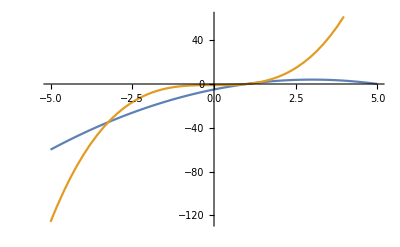

```mathematica
Plot[{6x-x^2-5,x^3-1},{x,-5,5}]
```

```mathematica
Solve[6x-x^2-5==x^3-1,x]
```

{{x→1},{x→-1-√5},{x→-1+√5}}

What if we want to know where 4x+by = 6 and ax+5y=9 for constants a, b ∈ ℝ?

Don’t do this:

```mathematica
Solve[{4*x+by==6,ax+5*y==9},{x,y}]
```

{{x→(6-by)/4,y→(9-ax)/5}}

Do this instead:

```mathematica
Solve[{4*x+b*y==6,a*x+5*y==9},{x,y}]
```

{{x→(3 (-10+3 b))/(-20+a b),y→(6 (-6+a))/(-20+a b)}}

Let’s try to find where x*arctan(x) = 5/9.

```mathematica
Solve[x*ArcTan[x]==5/9,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x ArcTan[x]==5/9,x]

```mathematica
NSolve[x*ArcTan[x]==5/9,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[x ArcTan[x]==5/9,x]

For NSolve we also have to specify the domain where our answer lives:

```mathematica
NSolve[x*ArcTan[x]==5/9,x,Reals]
```

{{x→-0.813501},{x→0.813501}}

## What is a differential equation?

We have an equation that can contain derivatives, independent variable terms, and dependent variable terms.
The solution to a differential equation is an expression (preferably solved for the dependent variable-- an explicit solution) relating the dependent variable and the independent variable. The solution does NOT contain derivatives.
E.g. let’s solve the differential equation 2y’’(x) + 3y’(x) + y(x) = cos(x) with no initial condition. Note that if a differential equation does not have specified initial conditions, the solution will depend on constants of integration (+C).

```mathematica
DSolve[2y''[x]+3y'[x]+y[x]==Cos[x],y[x],x]
```

{{y[x]→ⅇ^(-x/2) C[1]+ⅇ^-x C[2]+1/10 (-Cos[x]+3 Sin[x])}}

We talked about difference equations when we learned Excel--difference equations and differential equations are related.
difference eqn: future = present + change, e.g., y(n+1) = y(n) + change*Δt
differential eqn: derivative = instantaneous change, e.g. dy/dx = change.
SIR model as differential equations:
	dS/dt = -αS*I;
	dI/dt = αS*I - β*I;
	dR/dt = β*I;
	α, β ∈ ℝ.

```mathematica
answer=NDSolve[
{s'[t]==-0.005*s[t]*i[t],
i'[t]==0.005*s[t]*i[t]-0.2*i[t],
r'[t]==0.2*i[t],
s[0]==100,i[0]==1,r[0]==0},
{s[t],i[t],r[t]},
{t,0,60}
]
```

{{s[t]→InterpolatingFunction[…][t],i[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

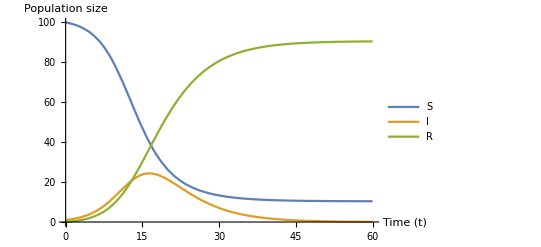

```mathematica
Plot[
{s[t]/.answer,i[t]/.answer,r[t]/.answer},
{t,0,60},
PlotLegends->{"S","I","R"},
AxesLabel->{"Time (t)", "Population size"}
]
```

To save picture and include the legend, we use Rasterize[ ]

```mathematica
Rasterize[Plot[
{s[t]/.answer,i[t]/.answer,r[t]/.answer},
{t,0,60},
PlotLegends->{"S","I","R"},
AxesLabel->{"Time (t)", "Population size"}
]]
```

-Graphics-

```mathematica
Manipulate[
answer2=NDSolve[
{s'[t]==-a*s[t]*i[t],
i'[t]==a*s[t]*i[t]-b*i[t],
r'[t]==b*i[t],
s[0]==100,i[0]==1,r[0]==0},
{s[t],i[t],r[t]},
{t,0,60}
];
Plot[
{s[t]/.answer2,i[t]/.answer2,r[t]/.answer2},
{t,0,60},
PlotLegends->{"S","I","R"},
AxesLabel->{"Time (t)", "Population size"}
],
{a,0.001,0.01},{b,0.01,0.5}
]
```